```mathematica
x=1/2(u^2-v^2)
y=u v
```

1/2 (u^2-v^2)

u v

```mathematica
A = {x y,y^2-x^2} //FullSimplify
```

{1/2 u (u-v) v (u+v),1/4 (-u^4+6 u^2 v^2-v^4)}

```mathematica
first = X == x
second =Y == y
```

X==1/2 (u^2-v^2)

Y==u v

```mathematica
rev = Solve[first&& second, {u,v}]// Expand //FullSimplify
```

{{u→-√(X-√(X^2+Y^2)),v→-Y/(√(X-√(X^2+Y^2)))},{u→√(X-√(X^2+Y^2)),v→Y/(√(X-√(X^2+Y^2)))},{u→-√(X+√(X^2+Y^2)),v→-Y/(√(X+√(X^2+Y^2)))},{u→√(X+√(X^2+Y^2)),v→Y/(√(X+√(X^2+Y^2)))}}

```mathematica
uBasis = {D[rev[[4,1,2]],X] //FullSimplify,D[rev[[4,1,2]],Y] //FullSimplify}
vBasis = {D[rev[[4,2,2]],X] //FullSimplify,D[rev[[4,2,2]],Y] //FullSimplify}
```

{(√(X+√(X^2+Y^2)))/(2 √(X^2+Y^2)),Y/(2 √(X^2+Y^2) √(X+√(X^2+Y^2)))}

{-Y/(2 √(X^2+Y^2) √(X+√(X^2+Y^2))),(√(X+√(X^2+Y^2)))/(2 √(X^2+Y^2))}

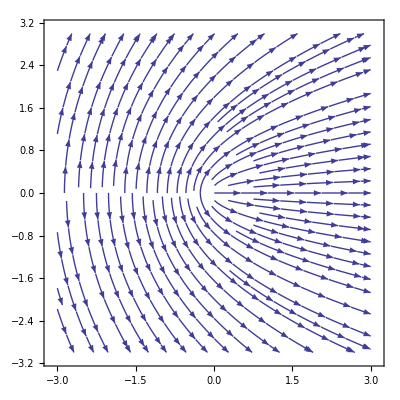

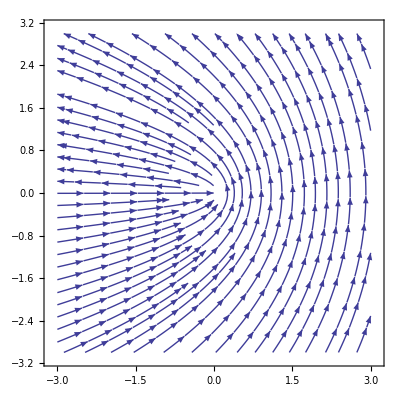

```mathematica
StreamPlot[uBasis,{X,-3,3},{Y,-3,3}]
StreamPlot[vBasis,{X,-3,3},{Y,-3,3}]
```

```mathematica
transU =du == D[rev[[4,1,2]],X] dx+ D[rev[[4,1,2]],Y] dy //FullSimplify
transV = dv==D[rev[[4,2,2]],X]dx +D[rev[[4,2,2]],Y]dy //FullSimplify
```

du==(dy Y+dx (X+√(X^2+Y^2)))/(2 √(X^2+Y^2) √(X+√(X^2+Y^2)))

dv==(√(X+√(X^2+Y^2)) (dy Y+dx (X-√(X^2+Y^2))))/(2 Y √(X^2+Y^2))

```mathematica
transXY = Solve[transU && transV, {dx,dy}] //FullSimplify
```

{{dx→(-dv Y+du (X+√(X^2+Y^2)))/(√(X+√(X^2+Y^2))),dy→(√(X+√(X^2+Y^2)) (dv Y+du (-X+√(X^2+Y^2))))/Y}}

```mathematica
transXY[[1,1,2]]
```

(-dv Y+du (X+√(X^2+Y^2)))/(√(X+√(X^2+Y^2)))

```mathematica
col = {transXY[[1,1,2]], transXY[[1,2,2]]}
```

{(-dv Y+du (X+√(X^2+Y^2)))/(√(X+√(X^2+Y^2))),(√(X+√(X^2+Y^2)) (dv Y+du (-X+√(X^2+Y^2))))/Y}

```mathematica
Aij = {{Y, -2X},{X,2Y}}
```

{{Y,-2 X},{X,2 Y}}

```mathematica
Aj = Aij.col //FullSimplify
```

{(du Y (-X+√(X^2+Y^2))-dv (Y^2+2 X (X+√(X^2+Y^2))))/(√(X+√(X^2+Y^2))),(dv Y (X+2 √(X^2+Y^2))+du (2 Y^2+X (X+√(X^2+Y^2))))/(√(X+√(X^2+Y^2)))}

```mathematica
FullSimplify[Ajtrans = Aj /. X -> x /. Y-> y , Assumptions->u ∈ Reals && v ∈ Reals]
```

{(-dv u^3+du v^3) Sign[u],1/2 (dv v (3 u^2+v^2)+du (u^3+3 u v^2)) Sign[u]}